# Evaluation

BX Pan
2017.9.18

There was some variability depending on the geo-graphical area. For instance, over Europe, the anomaly correlations decreased much quicker than over the Northern Hemisphere extratropics as a whole.

Miyakoda et al. (1986) used a 10-day running mean for both the forecasts and the observed data in an attempt to obtain positive skills by filtering out the unpredictable components, most especially the baroclinic eddies

“They were in effect arguing about artifacts induced by sampling at too low a resolution.”

phase shifts

## Evaluation

Deterministic Scores

Time Scale

Daily

Weekly

Spatial Scale

Grid

Area Average

Correlation Coefficient(r^2) and Root Mean Square Error(RMSE) are probably not the most suitable for assessing probabilistic forecasts after 10 days, but they are the most widely used for evaluating medium-range weather forecasting and they were used in previous papers on monthly forecasting. It should be Beat Climatology and Persistence (Molteni et al., 1986).

Example: BoM Dataset

#### Sample Collection

The Oct to Feb hindcasts for the West Coast CONUS were gathered as follows. Together there are 161 boreal winter months(33 years).

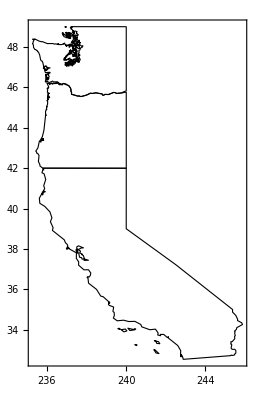

```mathematica
polygon=Block[{westconus},
	westconus=Block[{ow,ca},
	ow=Import["/Users/lambda/Documents/Data/GeoDivision/CONUS/oregonwashington.mx"];
	ca=Import["/Users/lambda/Documents/Data/GeoDivision/CONUS/california.mx"];
	Polygon[Flatten[{ow[[1]],ca[[1]]},1]]];
	westconus[[1]]];
(*polygon in the form of {subpoly1,subpoly2,...},subpoly in th form of {{long1,lat1},{long2,lat2}...}*)
Graphics[{EdgeForm[Black],FaceForm[None],Polygon[polygon]},Frame->True]
```

```mathematica
datasets=Block[{},
	SetDirectory["/Users/lambda/Documents/Research/S2SEvaluation/Data"];
	FileNames[][[{1,2,10,11,12,13,14,15,16,17,19}]]];
TableForm[Map[Block[{simu},
		SetDirectory["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>#];
		simu=Import[#<>"_simu.mx"];
		Flatten[{#,Dimensions[simu]}]]&,datasets],
		TableHeadings->{None,{"Dataset","Forecast Days","Ensemble Size","Starting Times","Grids"}},
		TableAlignments->Center]
```

Dataset | Forecast Days | Ensemble Size | Starting Times | Grids
BoM | 62 | 33 | 2376 | 13
CMA | 60 | 4 | 7665 | 33
ECCC | 32 | 4 | 1780 | 33
ECMWF | 46 | 11 | 2962 | 33
HCMR | 61 | 10 | 3268 | 33
ISACCNR | 31 | 1 | 2190 | 33
JMA | 34 | 5 | 1080 | 33
KMA | 60 | 3 | 660 | 33
MeteoFrance | 61 | 15 | 528 | 33
NCEP | 44 | 4 | 4380 | 33
UKMO | 60 | 3 | 1104 | 33

## Evaluation

```mathematica
EnsembleMeanEvaluate[dataset_,score_]:=Block[{simu,obser,msimu},
	{simu,obser}=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>dataset<>"/"<>dataset<>".mx"];
	msimu=Mean[simu];
	Table[Table[score[msimu[[;;,day,grid]],obser[[;;,day,grid]]],
		{day,Dimensions[obser][[2]]}],
		{grid,Dimensions[obser][[3]]}]];
```

```mathematica
colors={Red,Orange,Yellow,Pink,Brown,Green,Blue,Purple,Black,Gray,Cyan};
```

```mathematica
TableForm[Transpose[{datasets,colors}]]
```

BoM | RGBColor[1, 0, 0]
CMA | RGBColor[1, 0.5, 0]
ECCC | RGBColor[1, 1, 0]
ECMWF | RGBColor[1, 0.5, 0.5]
HCMR | RGBColor[0.6, 0.4, 0.2]
ISACCNR | RGBColor[0, 1, 0]
JMA | RGBColor[0, 0, 1]
KMA | RGBColor[0.5, 0, 0.5]
MeteoFrance | GrayLevel[0]
NCEP | GrayLevel[0.5]
UKMO | RGBColor[0, 1, 1]

```mathematica
NSE[simu_,obser_]:=1-Total[(simu-obser)^2]/Total[(obser-Mean[obser])^2];
```

```mathematica
RMSE[simu_,obser_]:=Sqrt[Mean[(simu-obser)^2]]
```

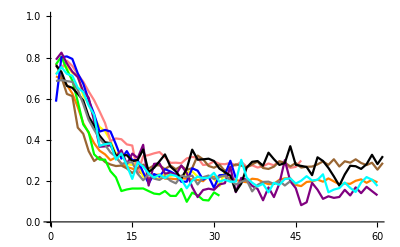
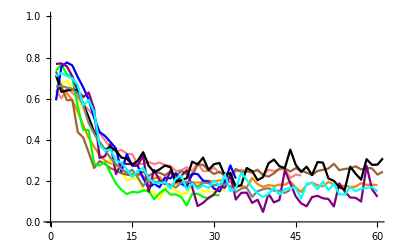
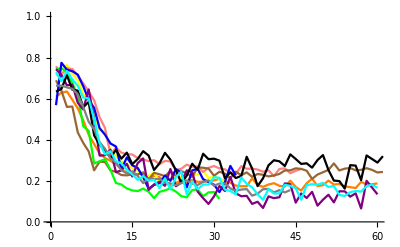
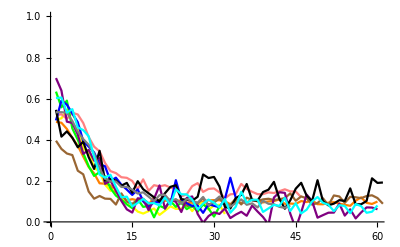
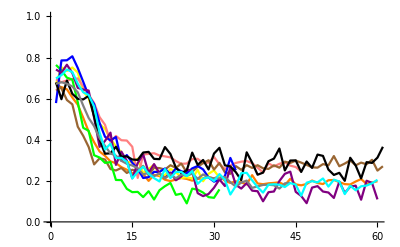
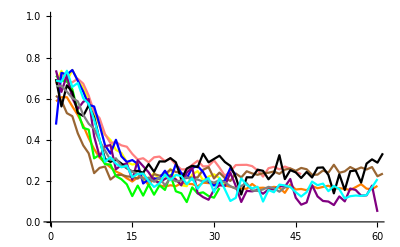
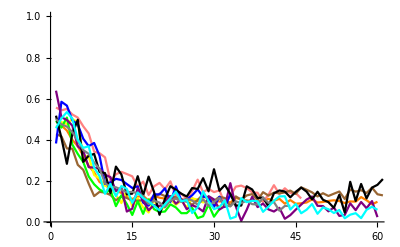
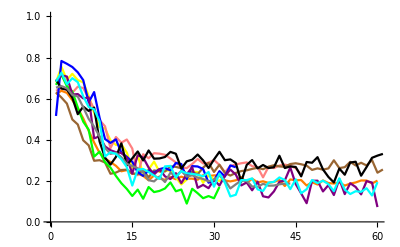

```mathematica
corr=Table[Show[Table[Block[{test=EnsembleMeanEvaluate[datasets[[i]],Correlation]},
	ListLinePlot[test[[grid]],
		PlotStyle->colors[[i]],
		PlotRange->{0,1}]],
	{i,2,11}]],{grid,31}]
```

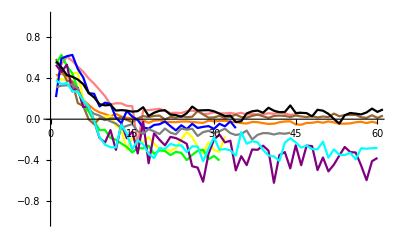
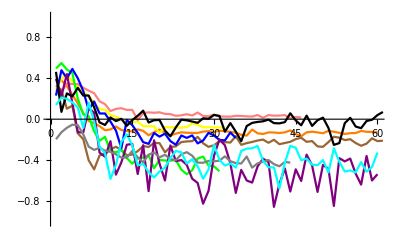
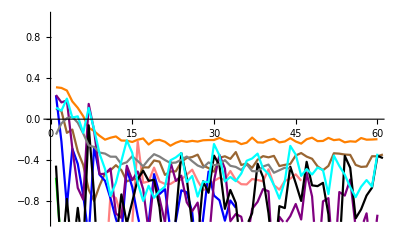
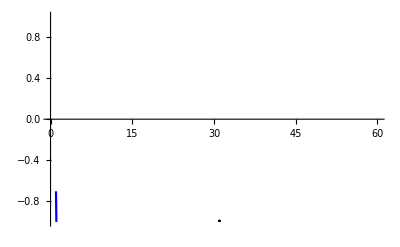
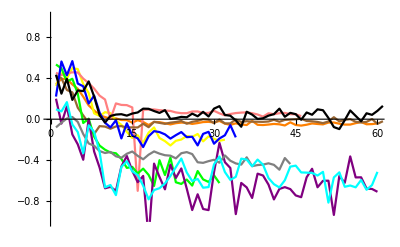
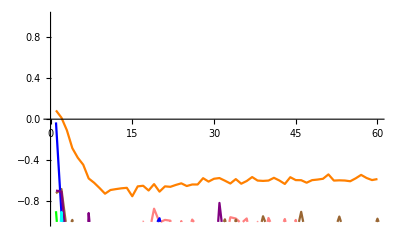
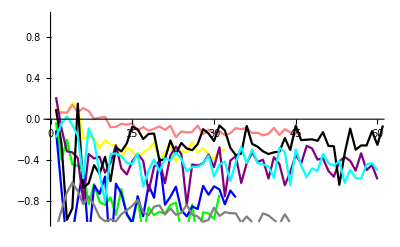
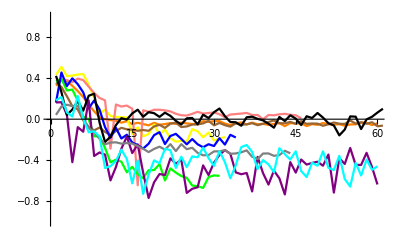

```mathematica
nse=Table[Show[Table[Block[{test=EnsembleMeanEvaluate[datasets[[i]],NSE]},
	ListLinePlot[test[[grid]],
		PlotStyle->colors[[i]],
		PlotRange->{-1,1}]],
	{i,2,11}]],{grid,31}]
```

```mathematica
rmse=Table[Show[Table[Block[{test=EnsembleMeanEvaluate[datasets[[i]],RMSE]},
	ListLinePlot[test[[grid]],
		PlotStyle->colors[[i]],
		PlotRange->{0,10}]],
	{i,2,11}]],{grid,31}]
```

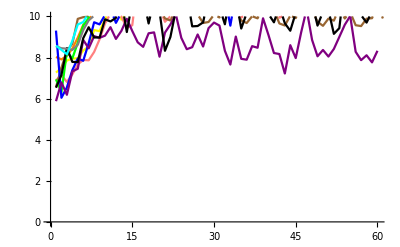
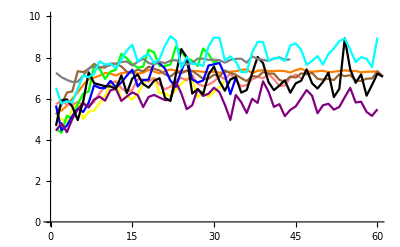
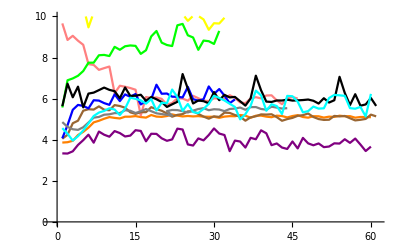
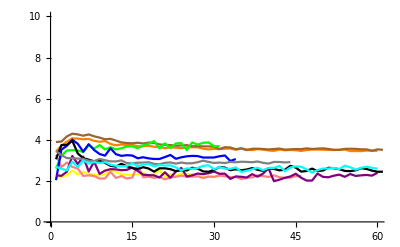
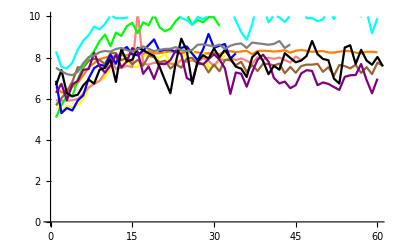
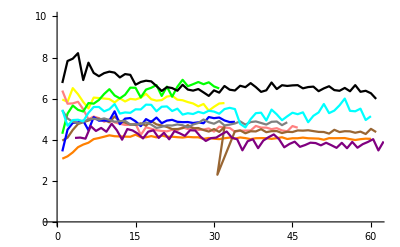
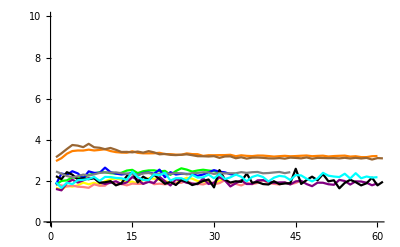
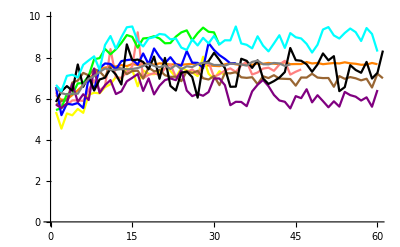

#### ReArrange

```mathematica
data=Block[{name="NCEP"},
	Import["/Users/lambda/Documents/Data/S2S/"<>name<>"/"<>name<>"_WestCONUS.mx"]];
```

```mathematica
SkillSequence[data_,score_]:=Block[{observation,simulation,size,grids,length,tempt,ensemble,Pmean,Pensemble},
	{size,tempt,grids,length}=Dimensions[data];
	ensemble=Dimensions[data[[1,2]]][[-1]];
	Pensemble=Table[Table[Table[score[data[[;;,1,grid,day]],data[[;;,2,grid,day,member]]],{day,length}],
		{grid,grids}],{member,ensemble}];
	Pmean=Table[Table[score[data[[;;,1,grid,day]],Map[Mean,data[[;;,2,grid,day]]]],{day,length}],{grid,grids}];
	{Pensemble,Pmean}];
```

```mathematica
RMSE[simu_,obser_]:=Sqrt[Mean[(simu-obser)^2.]];
score=Correlation;
{Pensemble,Pmean}=SkillSequence[data,score];
```

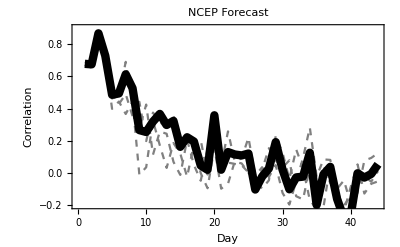

```mathematica
grid=8;
Show[{ListLinePlot[Pensemble[[;;,grid,;;]],PlotRange->{-0.2,0.9},PlotStyle->Table[{Gray,Dashed},Length[Pensemble]]],
ListLinePlot[Pmean[[grid,;;]],PlotStyle->{Thickness->0.015,Black}]},
Frame->True,
BaseStyle->20,
PlotLabel->"NCEP Forecast",
FrameLabel->{"Day",ToString[score]}]
```

Probabilistic Scores

#### Relative Operating Characteristics (ROC) Scores

The relative operating characteristics (ROC) scores are based on contingency tables giving the number of observed occurrences and nonoccurrences of an event as a function of the forecast occurrences and nonoccurrences of that event. The events are defined as binary, for instance, the probability that 2-m temperature is in the upper tercile. (Stanski et al. 1989; Mason and Graham 1999; Kharin and Zwiers 2003)

For each parameter value θi the point TPR (θi), FPR (θi) is plotted; points corresponding to consecutive θi' s are connected with a line. We call the obtained curve the ROC curve for the classifier in consideration. The ROC curve resides in the ROC space as defined by the functions FPR and TPR corresponding respectively to the x - axis and the y - axis.

#### Brier Skill Scores

#### Continuous Ranked Probability Skill Score

#### Reliability diagrams

#### Rank Histograms

#### Kullback-Leibler divergence

#### Taylor diagram

Dataset | Forecast Days | Ensemble Size | Starting Times | Grids
BoM | 62 | 33 | 2376 | 13
CMA | 60 | 4 | 7665 | 33
ECCC | 32 | 4 | 1780 | 33
ECMWF | 46 | 11 | 2962 | 33
HCMR | 61 | 10 | 3268 | 33
ISACCNR | 31 | 1 | 2190 | 33
JMA | 34 | 5 | 1080 | 33
KMA | 60 | 3 | 660 | 33
MeteoFrance | 61 | 15 | 528 | 33
NCEP | 44 | 4 | 4380 | 33
UKMO | 60 | 3 | 1104 | 33

```mathematica
dataset="ECMWF";
{simu, obser} = Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/" <> dataset <> "/" <> dataset <> ".mx"];
```

```mathematica
test=Table[Table[Table[Correlation[simu[[i,;;,j,grid]],obser[[;;,j,grid]]],
	{i,Dimensions[simu][[1]]}],{j,Dimensions[simu][[-2]]}],{grid,Dimensions[simu][[-1]]}];
```

```mathematica
Dimensions[test]
```

{31,46,11}

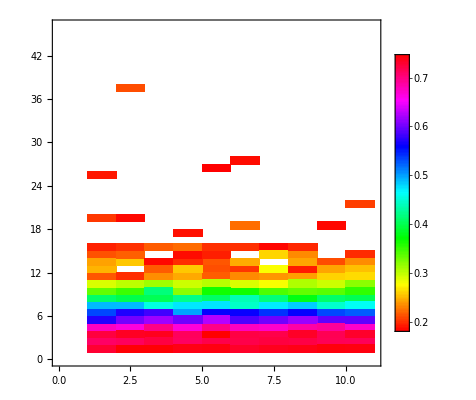
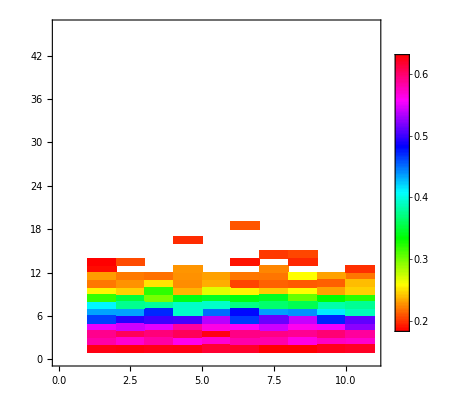
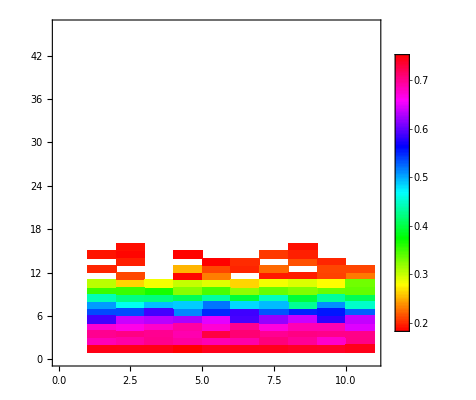
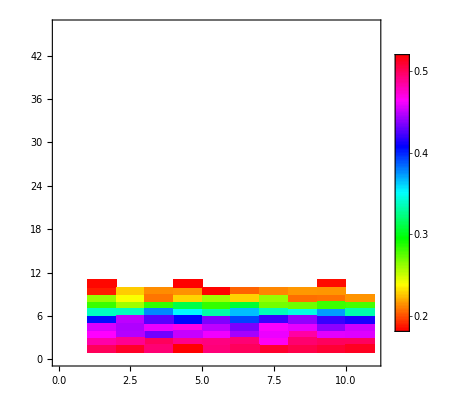
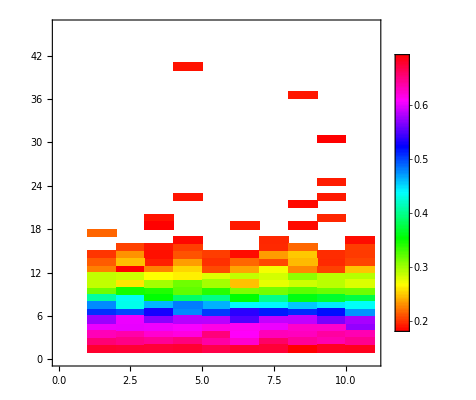
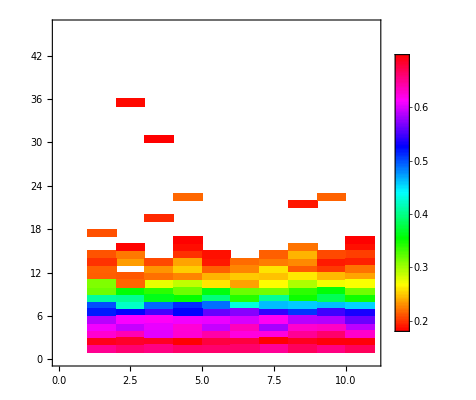
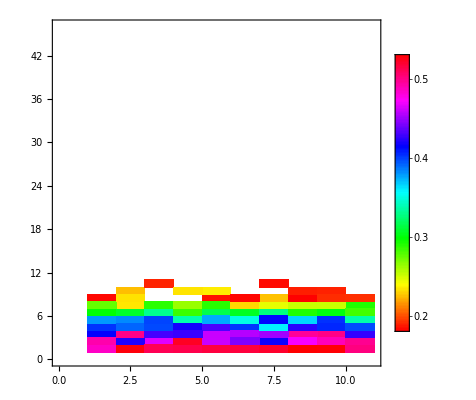
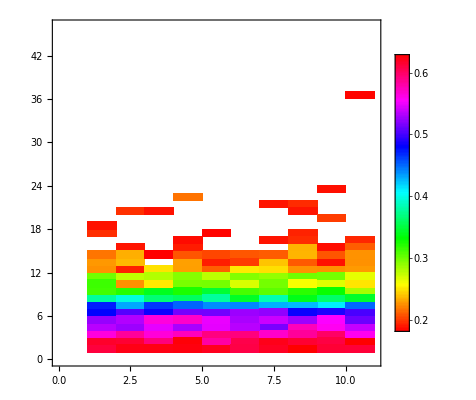

```mathematica
Map[ListDensityPlot[#,ColorFunction->Hue,
	PlotRange->{0.18,1},
	InterpolationOrder->0,
	PlotLegends->Automatic]&,test]
```

```mathematica
MinMax[simu]
MinMax[obser]
```

{0.,194.76}

{0.,109.076}

## History of Attempts

```mathematica
Tuples[{1, 2}, 2]
```

{{1,1},{1,2},{2,1},{2,2}}

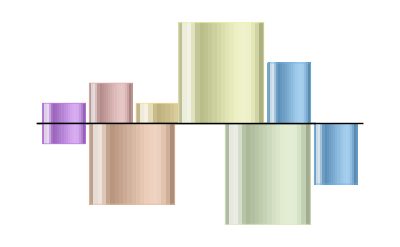

```mathematica
Rotate[Show[{RectangleChart[{{1,1},{1,2},{2,1},{2,-5},{1,-3}},
ChartElementFunction -> "GlassRectangle", ChartStyle -> "Pastel"],
	  RectangleChart[{{1,-1},{2,-4},{2,5},{1,3}}, 
	  ChartElementFunction -> "GlassRectangle", 
	  ChartStyle -> "Pastel"]},Axes->False],Pi/2]
```

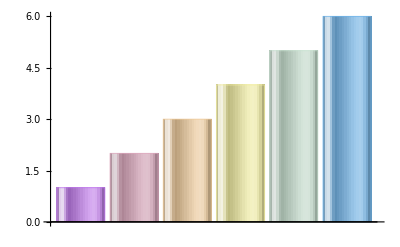

```mathematica
BarChart[Range[6], ChartElementFunction -> "GlassRectangle", 
ChartStyle -> "Pastel"]
```

-Graphics-

```mathematica
SetDirectory["/Users/lambda/Documents/Research/S2SEvaluation/Data/"]
FileNames[]
```

/Users/lambda/Documents/Research/S2SEvaluation/Data

{BoM_p,CMA_cp,.DS_Store,.DS_Store_control_time.mx,.DS_Store_control_time.mx_pertubation_time.mx,.DS_Store_control_time.mx_pertubation_time.mx_pertubation_time.mx,.DS_Store_pertubation_time.mx,.DS_Store_pertubation_time.mx_pertubation_time.mx,ECCC,ECMWF,HCMR_p,ISACCNR,JMA,KMA,MeteoFrance,NCEP,.tempt.sh.swp,UKMO}

```mathematica
dataset="UKMO";
SetDirectory["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>dataset];
control=Import["*_control.mx"];
pertubation=Import["*_pertubation.mx"];
If[Dimensions[control][[2]]==Dimensions[pertubation][[2]],
data=Table[Table[Table[Prepend[pertubation[[1,k,i,j]],control[[1,k,i,j]]],{j,Dimensions[control][[-1]]}],
	{i,Dimensions[control][[-2]]}],
	{k,Dimensions[control][[-3]]}];
Export[dataset<>"_mix.mx",data],dataset]
```

UKMO_mix.mx

```mathematica
ReScale[dataset_]:=Block[{data},
SetDirectory["/Users/lambda/Documents/Research/S2SEvaluation/Data/"<>dataset];
data=Import["*_mix.mx"][[1]];
data=Transpose[Table[If[i==1,data[[;;,;;,1,;;]],data[[;;,;;,i,;;]]-data[[;;,;;,i-1,;;]]],{i,Dimensions[data][[-2]]}]];
Export[dataset<>"_mix2.mx",data]]
```

```mathematica
Map[ReScale,{"ECCC","ECMWF","JMA","KMA","MeteoFrance","NCEP"}]
```

{ECCC_mix2.mx,ECMWF_mix2.mx,JMA_mix2.mx,KMA_mix2.mx,MeteoFrance_mix2.mx,NCEP_mix2.mx}

```mathematica
data=Import["/Users/lambda/Documents/Research/S2SEvaluation/Data/ECCC/ECCC_mix2.mx"];
```

```mathematica
Dimensions[data]
```

{2962,46,33,11}

```mathematica
MinMax[data]
```

{-0.0666085,276.876}

```mathematica
Dimensions[data]
```

{1780,32,33,4}

```mathematica
ListLinePlot[Transpose[data[[13,;;,3,;;]]],PlotRange->Full]
```

-Graphics-